```mathematica
ClearAll;
```

```mathematica
list[n_]:=FactorInteger[n][[All,1]];
ProductOdd[x_List, n_]:=Times@@((1-1/x^2)/(1-1/x^(n+1)));
ProductEven[x_List, n_]:=Times@@(1/((1-1/x^2)(1+1/x^(n+1))));
ProductLiouville[x_List]:=Times@@(1-1/x^2);
PrefactorOdd[j_]:=(-1)^((j+3)/2)((j+1)!)/(12BernoulliB[j+1](2π)^(j-1));
PrefactorEven[j_]:=(-1)^j(3Zeta[j+1](2(j+1))!)/(π^4 BernoulliB[2(j+1)](2π)^(2j));
COdd[j_,q_]:=PrefactorOdd[j]*ProductOdd[list[q], j];
CEven[j_,q_]:=PrefactorEven[j]ProductEven[list[q], j];
MuJ[j_,n_]:=If[Max[FactorInteger[n][[All,2]]]>=j+1,0,LiouvilleLambda[n]];
LK[k_,n_]:=DirichletConvolve[LiouvilleLambda[m],(Log[m])^k,m,n];
VarTheta[k_,x_,q_,a_]:=∑_(n=1)^x (If[GCD[a,q]==1,1,0]*If[Divisible[n-a,q]==True,1,0]*LK[k,n]);
LambdaJK[j_,k_,n_]:=∑_(d=1)^n If[Divisible[n,d],MuJ[j,d](Log[n/d])^k,0];
Psi[j_,k_,x_,q_,a_]:=∑_(n=1)^x (If[GCD[a,q]==1,1,0]*If[Divisible[n-a,q]==True,1,0]*LambdaJK[j,k,n]);
RHS11Odd[j_,k_,x_,q_,a_]:=k COdd[j,q]/EulerPhi[q]*x*(Log[x])^(k-1);
RHS11Even[j_,k_,x_,q_,a_]:=k CEven[j,q]/EulerPhi[q]*x*(Log[x])^(k-1);
RHS12[k_,x_,q_]:=k/EulerPhi[q]*π^2/6*ProductLiouville[list[q]]*x*(Log[x])^(k-1);
```

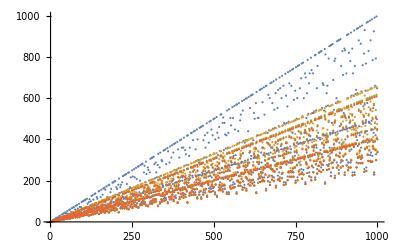

```mathematica
DiscretePlot[{EulerPhi[q]/COdd[1, q],EulerPhi[q]/COdd[3,q],EulerPhi[q]/COdd[5,q],EulerPhi[q]/COdd[7,q]},{q,2,1000},Filling->None]
```

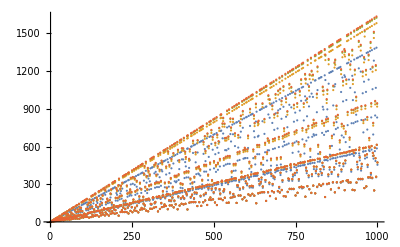

```mathematica
DiscretePlot[{EulerPhi[q]/CEven[2, q],EulerPhi[q]/CEven[4,q],EulerPhi[q]/CEven[6,q],EulerPhi[q]/CEven[8,q]},{q,2,1000},Filling->None]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

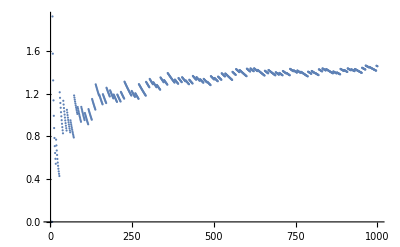

```mathematica
j=2;k=2;q=11;a=7;DiscretePlot[{Psi[j,k,x,q,a]/RHS11Even[j,k,x,q,a]},{x,1,1000},Filling->None]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

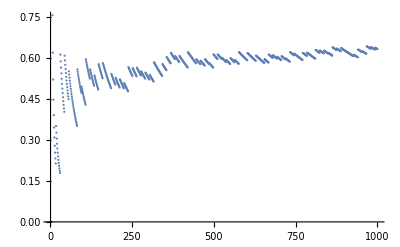

```mathematica
j=3;k=2;q=13;a=5;DiscretePlot[{Psi[j,k,x,q,a]/RHS11Odd[j,k,x,q,a]},{x,1,1000},Filling->None]
```

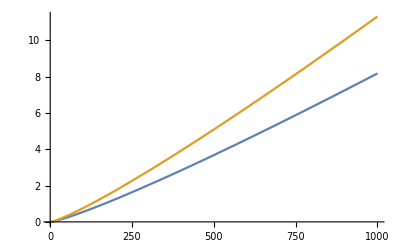

```mathematica
k=2;j=7;q=5000;a=5;Plot[{(RHS11Odd[j,k,x,q,a]),(PrefactorOdd[j]/EulerPhi[q] 2x Log[x]) },{x,1,1000},Filling->None]
```

```mathematica
k=2;
j=12;
q=5000;
a=7;
```

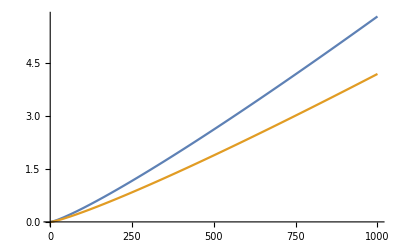

```mathematica
Plot[{RHS11Even[j,k,x,q,a],PrefactorEven[j]/EulerPhi[q] 2x Log[x]},{x,1,1000},Filling->None]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

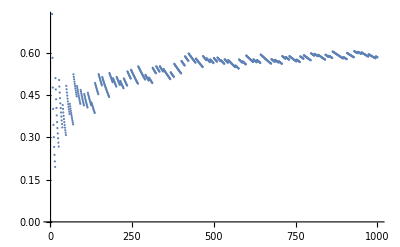

```mathematica
k=2;q=11;a=5;DiscretePlot[{VarTheta[k,x,q,a]/RHS12[k,x,q]},{x,1,1000},Filling->None]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

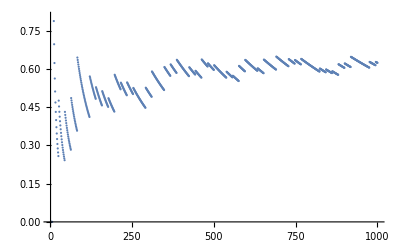

```mathematica
k=2;q=19;a=7;DiscretePlot[{VarTheta[k,x,q,a]/RHS12[k,x,q]},{x,1,1000},Filling->None]
```

```mathematica
j=2;k=2;q=11;a=7;x=100000;DiscretePlot[{Psi[j,k,x,q,a],RHS11Even[j,k,x,q,a]},{q,1,Log[x]},Filling->None]
```

$Aborted

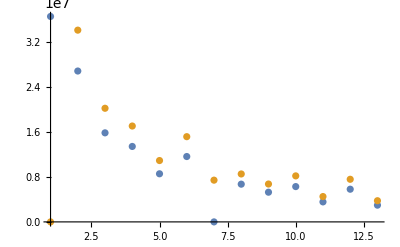

```mathematica
k=2;a=7;x=1000000;DiscretePlot[{VarTheta[k,x,q,a],RHS12[k,x,q]},{q,1,Log[x]},Filling->None]
```

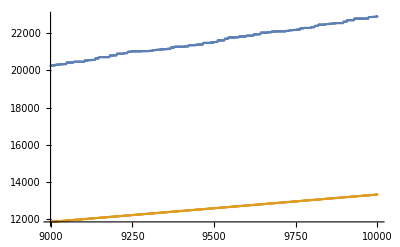

```mathematica
j=2;k=2;q=11;a=7;DiscretePlot[{Psi[j,k,x,q,a],RHS11Even[j,k,x,q,a]},{x,9000,10000},Filling->None]
```

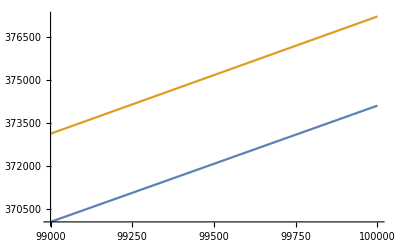

```mathematica
k=2;j=7;q=11;a=5;Plot[{RHS11Odd[j,k,x,q,a],PrefactorOdd[j]/EulerPhi[q] 2x Log[x] },{x,99000,100000},Filling->None]
```

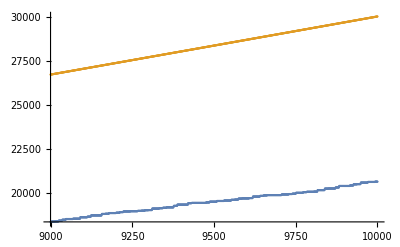

```mathematica
k=2;q=11;a=5;DiscretePlot[{VarTheta[k,x,q,a],RHS12[k,x,q]},{x,9000,10000},Filling->None]
```

```mathematica
k=2;j=7;q=5000;a=5;Plot[{(RHS11Odd[j,k,x,q,a]),(PrefactorOdd[j]/EulerPhi[q] 2x Log[x]) },{x,1,1000},Filling->None]
```

-Graphics-

```mathematica
k=2;
j=12;
q=13;
a=7;
```

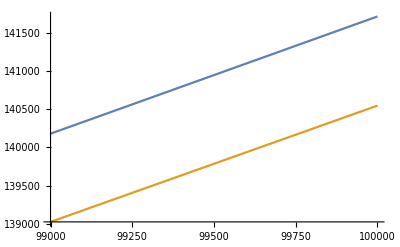

```mathematica
Plot[{RHS11Even[j,k,x,q,a],PrefactorEven[j]/EulerPhi[q] 2x Log[x]},{x,99000,100000},Filling->None]
```